```mathematica
f=Sqrt[1+dy^2]/Sqrt[2 g y]
f=Sqrt[1+dx^2]/Sqrt[2 g y]
D[f,y]-D[D[f,dy],x]
D[f,y]
Needs["VariationalMethods`"]
EulerEquations[√((x'[t]^2+y'[t]^2)/(2g y[t])),{x[t],y[t]},t]
```

(√(1+dy^2))/(√2 √(g y))

(√(1+dx^2))/(√2 √(g y))

-(√(1+dx^2) g)/(2 √2 (g y)^(3/2))

-(√(1+dx^2) g)/(2 √2 (g y)^(3/2))

{(y'[t] (x'[t]^3-2 y[t] y'[t] x''[t]+x'[t] (y'[t]^2+2 y[t] y''[t])))/(2 √2 g^2 y[t]^3 ((x'[t]^2+y'[t]^2)/(g y[t]))^(3/2))==0,-(x'[t] (x'[t]^3-2 y[t] y'[t] x''[t]+x'[t] (y'[t]^2+2 y[t] y''[t])))/(2 √2 g^2 y[t]^3 ((x'[t]^2+y'[t]^2)/(g y[t]))^(3/2))==0}

```mathematica
f=Sqrt[1+dx^2]/Sqrt[2 g y]
Integrate[f,{y,0,y1}]
```

(√(1+dx^2))/(√2 √(g y))

(√2 √(1+dx^2) y1)/(√(g y1))

```mathematica
D[a x^4+b x^3 +c x^2+d x +e,x]
```

d+2 c x+3 b x^2+4 a x^3

```mathematica
veceqs={};
For[i=1,i≤10,i++,
eqx=a x^4+b x^3 +c x^2+d x +e;
eq[x_]:=a x^4+b x^3 +c x^2+d x +e;
deq[x_]:=d+2 c x+3 b x^2+4 a x^3;
sol=Solve[{eq[0]==1,eq[1]==0.7,deq[0]==RandomReal[{-1,1}],deq[1]==RandomReal[{-1,1}],eq[0.5]==RandomReal[{0,1}]},{a,b,c,d,e}][[1]];
eqx=eqx/.sol;
AppendTo[veceqs,eqx];
];
```

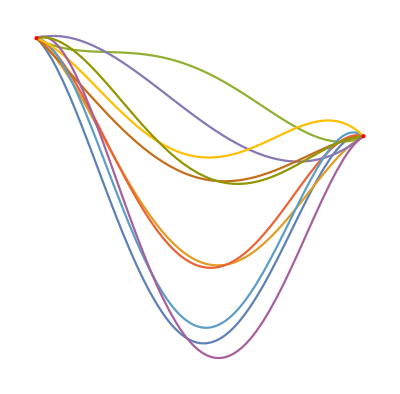

1.07408

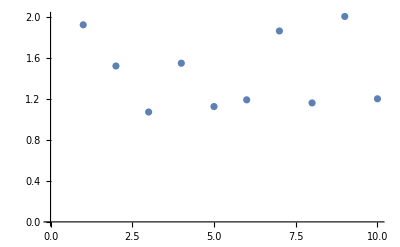

```mathematica
gph=Graphics[{PointSize[Large],Red,Point[{1,0.7}]}];
gph2=Graphics[{PointSize[Large],Red,Point[{0,1}]}];
lp=Plot[veceqs,{x,0,1}];
Show[gph,lp,gph2]
ints=Table[NIntegrate[Sqrt[1+D[veceqs[[i]],x]^2],{x,0,1}],{i,1,Length[veceqs]}];
Min[ints]
ListPlot[ints,AxesOrigin->{0,0}]
```

```mathematica
Integrate[Sqrt[y+y D[y,x]^2]/y,{y,y1,y2}]
```

```mathematica
Sqrt[y+y D[y,x]^2]/y
```

1/(√y)

```mathematica
D[y,x]^2
```

0

```mathematica
Sqrt[1+ D[y,x]^2]/Sqrt[y]
```

1/(√y)

```mathematica
Sqrt[y+y D[y,x]^2]/y
```

1/(√y)

```mathematica
D[Sqrt[y+y D[y[x],x]^2]/y,y]
```

(1+y'[x]^2)/(2 y √(y+y y'[x]^2))-(√(y+y y'[x]^2))/y^2

```mathematica
f=Sqrt[1+ D[y[x],x]^2]/Sqrt[y]
D[f,y]
```

(√(1+y'[x]^2))/(√y)

-(√(1+y'[x]^2))/(2 y^(3/2))

```mathematica
D[Sqrt[1+ y'[x]^2],y]
```

0

```mathematica
a=D[Sqrt[1+y'[x]^2]/Sqrt[y[x]],y[x]]
b=D[Sqrt[1+y'[x]^2]/Sqrt[y[x]],y'[x]]
c=D[b,x]
Simplify[a-c]
```

-(√(1+y'[x]^2))/(2 y[x]^(3/2))

y'[x]/(√y[x] √(1+y'[x]^2))

-y'[x]^2/(2 y[x]^(3/2) √(1+y'[x]^2))-(y'[x]^2 y''[x])/(√y[x] (1+y'[x]^2)^(3/2))+y''[x]/(√y[x] √(1+y'[x]^2))

(-1-y'[x]^2-2 y[x] y''[x])/(2 y[x]^(3/2) (1+y'[x]^2)^(3/2))

```mathematica
Integrate[(-1-y'[x]^2-2 y[x] y''[x])/(2 y[x]^(3/2) (1+y'[x]^2)^(3/2)),{y[x],0,1}]
```

(1+y'[x]^2-2 y[x] y''[x])/(√y[x] (1+y'[x]^2)^(3/2))